# GRADOS EN INGENIERÍA TELEMÁTICA E INGENIERÍA DE TECNOLOGÍAS DE TELECOMUNICACIÓN Métodos Matemáticos de las Telecomunicaciones (curso 23 - 24) Práctica 3 (3 de 3). Desarrollo en serie de Fourier.

## Representación de algunos trozos de funciones periódicas.

Sea la función f(t) de periodo T como la siguiente (en la que solo dibujamos dos trozos de la curva):

-Graphics-

lo normal es que dicha función se exprese solo en una de las partes, por ejemplo, f(t) con a≤t<b y decir que se repite por periodicidad. En este caso, al intervalo [a,b) se llama intervalo principal.

En cada trozo [a,b), [b,b+T),... la función f(t) tiene una expresión diferente (aunque tenga la misma forma geométrica).

La clave para definir en cada uno de los trozos una función como la anterior se encuentra en el siguiente esquema:

-Graphics-

Si llamamos fip(t) a la expresión de f(t) en el intervalo principal [a,b), entonces, para el siguiente intervalo t∈[b,b+T):

f(t)=fip(t-T)

## Ejercicio 1

Sea la función periódica:

f(t)=Piecewise[{{2t, -1≤t<1}, {, en el resto por periodicidad}}]

Dar la expresión de f(t) en el intervalo [-3,5) y representarla gráficamente.

## Desarrollo en serie de Fourier de una función periódica f(t).

Sea f(t) T-periódica (la frecuencia circular de f(t) será ω=(2π)/T), el desarrollo en serie de Fourier de f(t), que se suele escribir como F(t), será la siguiente serie funcional:

F(t)=a_0/2+∑_(n=1)^∞ (a_n cos(n ω t)+b_n sen(n ω t))

donde a_0, a_n y b_n se denominan coeficientes de Fourier y tienen la siguiente expresión:

Piecewise[{{a_0=2/T∫_d^(d+T) f(t)ⅆt, }, {a_n=2/T∫_d^(d+T) f(t)cos(n ω t)ⅆt, }, {b_n=2/T∫_d^(d+T) f(t)sen(n ω t)ⅆt, }}]

donde d puede ser cualquier número. En la práctica, el intervalo [d,d+T) será el intervalo principal de f(t).

## Ejercicio 2

Sea la función f(t) que en el intervalo principal [-1,1) está definida por:

f(t)=Piecewise[{{-t, -2≤t<0}, {t, 0≤t<2}, {, en el resto por periodicidad}}]

Se pide:
a) El periodo de f(t).
b) La frecuencia circular de f(t).
c) Los coeficientes de Fourier de f(t).
d) La suma parcial S_2(t) de orden 2 del desarrollo en serie de Fourier de f(t).
e) Un dibujo, sobre los mismos ejes, de f(t) (en el intervalo principal y los intervalos contiguos) y de S_2(t).
f) Calcular una aproximación del valor de f(8.2).

Which[-2≤t<0,-t,0≤t<2,t]

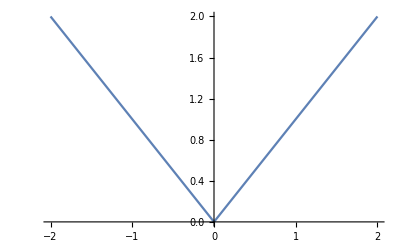

```mathematica
f[t_] = Which[-2 <=t< 0, -t, 0 <=t<2, t]
Plot[f[t], {t,-2,2}]
```

A)

```mathematica
T = 2 - (-2)
```

4

B)

```mathematica
W = (2Pi) / T
```

π/2

C)

```mathematica
a[n_] = 2/T(∫_-2^2 f[t] * Cos[n*W*t]ⅆt)
```

(4 (-1+Cos[n π]+n π Sin[n π]))/(n^2 π^2)

```mathematica
Simplify[%, n ∈ Integers && n > 0]
```

(4 (-1+(-1)^n))/(n^2 π^2)

```mathematica
b[n_] = 2/T(∫_-2^2 f[t] * Sin[n*W*t]ⅆt)
```

0

Luego, efectivamente, al tratarse de una función par, los Bn = 0

D)

```mathematica
S2[t_] = a[0] /2 + ∑_(n=1)^2 (a[n] * Cos[n*W*t]+ b[n] * Sin[n*W*t])
```

1-(8 Cos[(π t)/2])/π^2

E)

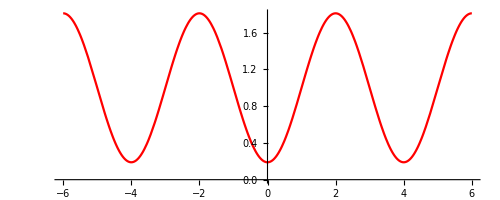

```mathematica
d1 = Plot[S2[t], {t,-6,6}, AspectRatio->Automatic, PlotStyle->Red]
```

```mathematica
f2[t_] := Which[-2 <= t < 2, f[t], 2 <= t < 6, f[t - T], -6 <= t <2, f[t + T]]
```

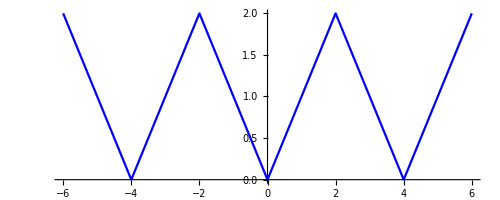

```mathematica
d2 = Plot[f2[t], {t,6,-6}, AspectRatio->Automatic, PlotStyle->Blue]
```

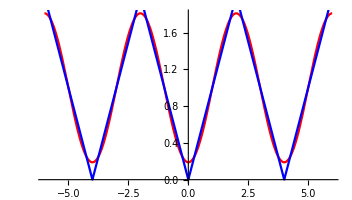

```mathematica
Show[d1,d2]
```

F)

```mathematica
S2[8.2]
```

0.229103

## Ejercicio 3

Calcular la suma parcial de orden 5 del desarrollo en serie De Fourier de la función:
				f(t)=Piecewise[{{t cos t, -π≤ t <π}, {, resto por periodicidad}}]

```mathematica
Clear["Global`*"]
```

```mathematica
f[t_] =  Which[-Pi<=t< Pi, t*Cos[t]]
```

Which[-π≤t<π,t Cos[t]]

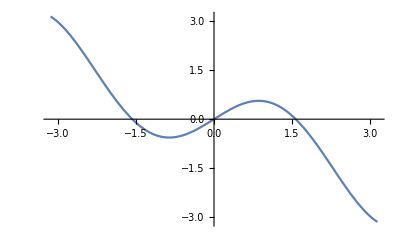

```mathematica
Plot[f[t],{t, -Pi, Pi}]
```

```mathematica
T = 2Pi
```

2 π

```mathematica
W = (2Pi)/(2Pi)
```

1

```mathematica
a[n_] = 2/T(∫_-Pi^Pi f[t] * Cos[n*W*t]ⅆt)
```

0

```mathematica
Simplify[a[n], n ∈ Integers && n > 0]
```

a[n]

```mathematica
b[n_] = 2/T(∫_-Pi^Pi f[t] * Sin[n*W*t]ⅆt)
```

(2 (-n π Cos[n π]+n^3 π Cos[n π]-Sin[n π]-n^2 Sin[n π]))/((-1+n^2)^2 π)

```mathematica
Simplify[b[n], n ∈ Integers && n > 0]
```

(2 (-1)^n n)/(-1+n^2)

```mathematica
S5[t_] = a∑_(n=2)^5 ( b[n] * Sin[n*W*t])
```

a (4/3 Sin[2 t]-3/4 Sin[3 t]+8/15 Sin[4 t]-5/12 Sin[5 t])

```mathematica
b1 = 2/T(∫_-Pi^Pi f[t] * Sin[n*W*t]ⅆt)
```

(2 (-n π Cos[n π]+n^3 π Cos[n π]-Sin[n π]-n^2 Sin[n π]))/((-1+n^2)^2 π)

## Expresión compleja de la serie de Fourier.

En la Guía de prácticas se comenta que hay otra forma de expresar la serie de Fourier utilizando variable compleja que, por otra parte, es muy utilizada en los textos de ingeniería por ser una expresión muy simple y compacta.

La expresión compleja es:

F(t)=∑_(n=-∞)^∞ (c_n ⅇ^(ⅈ n ω t))

con:

{c_0=1/T ∫_d^(d+T) f(t)ⅆt                
c_n=1/T ∫_d^(d+T) f(t)ⅇ^(-ⅈ n ω t)ⅆt

Nota 1. Hay que señalar que, ahora, n toma valores positivos y negativos.
Nota 2. Aunque se utiliza la exponencial compleja, el resultado sigue siendo una suma de funciones reales.

## Ejercicio 4

En el ejercicio 2 se comprobó que la suma parcial de orden 2 del desarrollo en serie de Fourier de la función:

f(t)=Piecewise[{{-t, -2≤t<0}, {t, 0≤t<2}, {, en el resto por periodicidad}}]

era:

1-(8 Cos[(π t)/2])/π^2

Obtener este resultado mediante la expresión compleja de la serie de Fourier.